## Coupled VAE Analysis

### Input Maximum Likelihood Data

```mathematica
CVAEFolder = "/Users/kenricnelson/Documents/Wolfram Mathematica/Coupled VAE/Rcode/";
```

```mathematica
CoupledVAEData=Exp[Flatten[
Import[CVAEFolder<>"ml"<>#<>"_alpha2","CSV"]
]&/@{"0","025","005","01"}
]
```

{{4.0174479590083631×10^-32,2.6869914090653067×10^-38,3.828901172625566×10^-47,4995,1.4341824031247758×10^-39,1.197150742890112×10^-20},2,{37,4998,48}}
 |  |  |  |

### Define LikelihoodHistogram

```mathematica
Clear[LikelihoodHistogram,AccuracyPlot,AccuracyMetrics];
LikelihoodHistogram[x_]:=Module[{HistRange={0.35,1600 }},Show[
Histogram[x,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},HistRange},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold],
ChartElementFunction->"EdgeFadingRectangle"
],
AccuracyPlot[AccuracyMetrics[x]]
]];
AccuracyPlot[x_]:=Module[{HistRange={0.37,1600 }},ListLogLogPlot[{
Labeled[{x⟦1⟧,HistRange⟦2⟧-1500},"Robustness",Above],
Labeled[{x⟦2⟧,HistRange⟦2⟧-350},"Accuracy ", Above],
Labeled[{x⟦3⟧,HistRange⟦2⟧-1000}," Decisiveness",Above]
},
LabelStyle->Directive[Medium, Blend[{Blue,Gray},0.75],Bold],
Filling->HistRange⟦1⟧,
FillingStyle->Thick,
PlotMarkers->{Automatic,.1}
]];
AccuracyMetrics[x_]:=
WeightedGeneralizedMean[x,#]&/@{-3/2,0,1};
```

### Plots

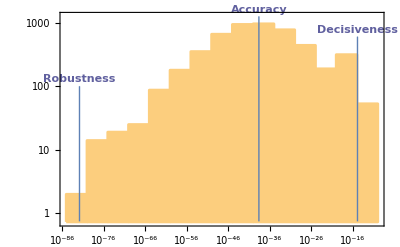

```mathematica
LikelihoodHistogram[CoupledVAEData⟦1,All⟧]
```

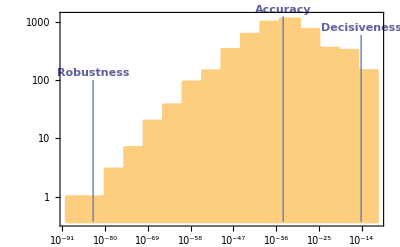

```mathematica
LikelihoodHistogram[CoupledVAEData⟦2,All⟧]
```

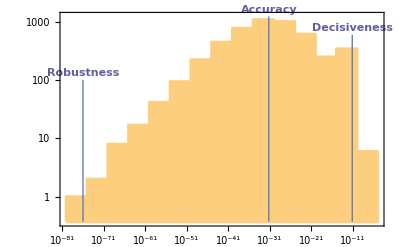

```mathematica
LikelihoodHistogram[CoupledVAEData⟦3,All⟧]
```

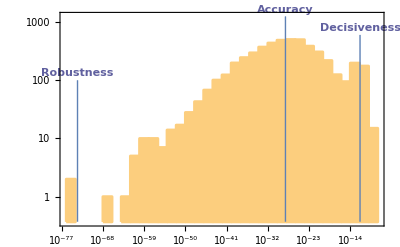

```mathematica
LikelihoodHistogram[CoupledVAEData⟦4,All⟧]
```

### Draft Functions

```mathematica
Clear[LikelihoodHistogram];
LikelihoodHistogram[x_]:=Show[
Histogram[x,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},{.7,1500}},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold],
ChartElementFunction->"EdgeFadingRectangle"
],
AccuracyPlot[AccuracyMetrics[x]]
];
AccuracyPlot[x_]:=ListLogLogPlot[{
Labeled[{x⟦1⟧,1000},"Robustness",Above],
Labeled[{x⟦2⟧,1000},"Accuracy", Above],
Labeled[{x⟦3⟧,1000},"Decisiveness",Above]
},
LabelStyle->Directive[Medium, Blend[{Blue,Gray},0.75],Bold],
Filling->0.75,
FillingStyle->Thick,
PlotMarkers->{Automatic,.1}
];
AccuracyMetrics[x_]:=
WeightedGeneralizedMean[x,#]&/@{-3/2,0,1};
```

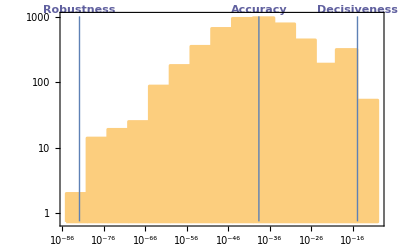

```mathematica
LikelihoodHistogram[LikelihoodKappa0Alpha2]
```

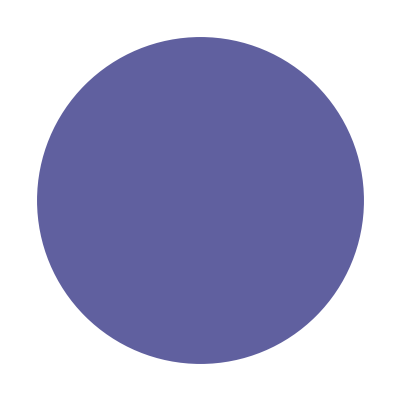

```mathematica
Graphics[{Blend[{Blue,Gray},0.75],Disk[]}]
```

```mathematica
SaveAccMet=AccuracyMetrics[LikelihoodKappa0Alpha2];
```

```mathematica
Clear[AccuracyPlot];
AccuracyPlot[x_]:=ListLogLogPlot[{
Labeled[{x⟦1⟧,1000},"Robustness",Right],
Labeled[{x⟦2⟧,1000},"Accuracy",Right],
Labeled[{x⟦3⟧,1000},"Decisiveness",Right]
},
LabelStyle->Directive[Medium, Bold],
Filling->Bottom,
FillingStyle->Thick,
PlotMarkers->{Automatic,.1}];
```

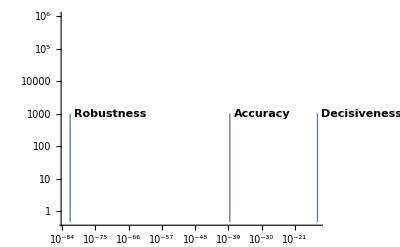

```mathematica
AccuracyPlot[SaveAccMet]
```

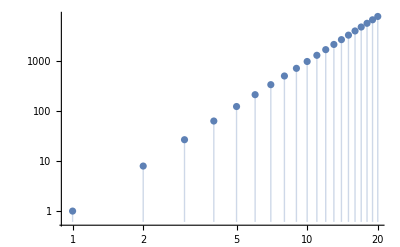

```mathematica
ListLogLogPlot[Range[20]^3,Filling->Bottom]
```

```mathematica
LikelihoodHistogram[x_]:=Histogram[x,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},{.7,1000}},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold]
];
AccuracyMetrics[x_]:=
WeightedGeneralizedMean[x,#]&/@{-3/2,0,1};
```

```mathematica
AccuracyPlot[x_]:=ListLinePlot[{
Labeled[{{x⟦1⟧,0.7},{x⟦1⟧,1000}},"Robustness"],
Labeled[{{x⟦2⟧,0.7},{x⟦2⟧,1000}},"Accuracy"],
Labeled[{{x⟦3⟧,0.7},{x⟦3⟧,1000}},"Decisiveness"]
}];
```

```mathematica
AccuracyPlot[AccuracyMetrics[LikelihoodKappa0Alpha2]]
```

-Graphics-

```mathematica
AccuracyMetrics[LikelihoodKappa0Alpha2]
```

{1.5598×10^-82,2.41385×10^-39,1.31033×10^-15}

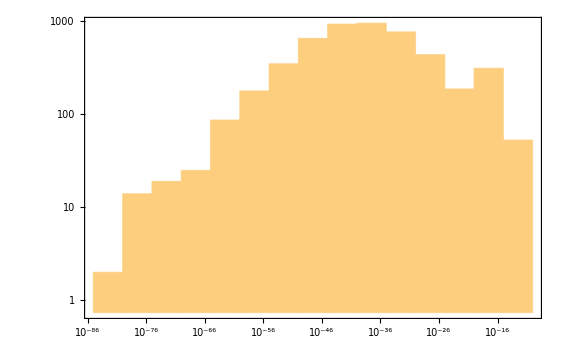

```mathematica
Histogram[LikelihoodKappa0Alpha2,"Log", 
PlotTheme->"Detailed",
ScalingFunctions->{"Log","Log"},
PlotRange->{{10^-100,10^-1},{.7,1000}},
AxesOrigin->{10^-100,10^-5},
FrameStyle->Directive[Black,Medium, Bold]
]
```

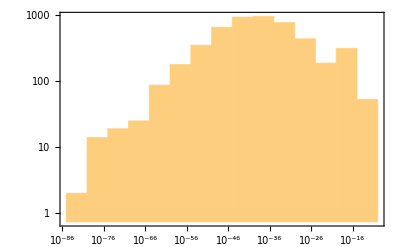

```mathematica
Show[%50,Axes->True,AxesStyle->Black]
```

```mathematica
Histogram[LikelihoodKappa0Alpha2,"Log",PlotTheme->"Detailed",ScalingFunctions->{"Log","Log"},PlotRange->{{1/100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,1/10000000000},{1,1000}},AxesOrigin->{1/10000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,1/100000}]
```

-Graphics-

```mathematica
ChartElementData["Histogram"]
```

{ArrowRectangle,EdgeFadingRectangle,FadingRectangle,GlassRectangle,GradientRectangle,GradientScaleRectangle,ObliqueRectangle,Rectangle,SegmentScaleRectangle}

```mathematica
ChartElementData["BarChart"]
```

{ArrowRectangle,EdgeFadingRectangle,FadingRectangle,GlassRectangle,GradientRectangle,GradientScaleRectangle,ObliqueRectangle,Rectangle,SegmentScaleRectangle}

## Coupled Divergence for the VAE

```mathematica
$Assumptions={μPost,σPost,μPrior,σPrior,μPost1,μPost2,σPost1,σPost2,κDiv}∈Reals&&0<μPost<∞&&0<σPost<∞&&0<μPrior<∞&&0<σPost<∞&&0<κDiv<∞;
```

### One Dimensional Case

```mathematica
CoupledDivergence[NormalDistribution[μPost,σPost], NormalDistribution[0,σPrior],κDiv]
```

```mathematica
-(-1+(2 π)^(κDiv/(1+κDiv)) √((1+3 κDiv)/(1+κDiv)) σPost^((2 κDiv)/(1+κDiv)))/(2 κDiv)+(Piecewise[{{(ⅇ^(-((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) (-2^(1+κDiv/(1+κDiv)) ⅇ^((μPost+3 κDiv μPost)^2/((1+κDiv) σPost^2 (2+κDiv (6-(4 σPost^2)/σPrior^2)))) π^(κDiv/(1+κDiv)) √((1+κDiv)^2 (1+3 κDiv)) (-σPrior)^((2 κDiv)/(1+κDiv)) σPrior-3 ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2)-3 ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) κDiv √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2)+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) Erf[(√((1+3 κDiv)/(1+κDiv)) μPost)/(√2 σPost)]+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) κDiv √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) Erf[(√((1+3 κDiv)/(1+κDiv)) μPost)/(√2 σPost)]+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) GammaRegularized[1/2,((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)]+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) κDiv √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) GammaRegularized[1/2,((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)]))/(4 κDiv (1+κDiv) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2)), σPrior<0}, {(ⅇ^(-((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) (2^(1+κDiv/(1+κDiv)) ⅇ^((μPost+3 κDiv μPost)^2/((1+κDiv) σPost^2 (2+κDiv (6-(4 σPost^2)/σPrior^2)))) π^(κDiv/(1+κDiv)) √((1+κDiv)^2 (1+3 κDiv)) σPrior^(1+(2 κDiv)/(1+κDiv))-3 ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2)-3 ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) κDiv √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2)+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) Erf[(√((1+3 κDiv)/(1+κDiv)) μPost)/(√2 σPost)]+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) κDiv √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) Erf[(√((1+3 κDiv)/(1+κDiv)) μPost)/(√2 σPost)]+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) GammaRegularized[1/2,((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)]+ⅇ^(((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)) κDiv √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2) GammaRegularized[1/2,((1+3 κDiv) μPost^2)/(2 (1+κDiv) σPost^2)]))/(4 κDiv (1+κDiv) √(-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2)), σPrior>0}, {0, True}}])//FullSimplify
```

(1-(2 π)^(κDiv/(1+κDiv)) √(3-2/(1+κDiv)) σPost^((2 κDiv)/(1+κDiv))+2 κDiv (Piecewise[{{(-1+(ⅇ^((κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2))) (2 π)^(κDiv/(1+κDiv)) (-σPrior)^(1+(2 κDiv)/(1+κDiv)))/(√(-(2 κDiv σPost^2)/(1+3 κDiv)+σPrior^2)))/(2 κDiv), σPrior<0}, {(-1+(ⅇ^((κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2))) (2 π)^(κDiv/(1+κDiv)) σPrior^(1+(2 κDiv)/(1+κDiv)))/(√(-(2 κDiv σPost^2)/(1+3 κDiv)+σPrior^2)))/(2 κDiv), σPrior>0}, {0, True}}]))/(2 κDiv)

```mathematica
(2 π)^(κDiv/(1+κDiv))/(2 κDiv)( √(3-2/(1+κDiv)) σPost^((2 κDiv)/(1+κDiv))+(ⅇ^((κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (-2 κDiv σPost^2+σPrior^2+3 κDiv σPrior^2)))  σPrior^(1+(2 κDiv)/(1+κDiv)))/(√(-(2 κDiv σPost^2)/(1+3 κDiv)+σPrior^2)) )
```

Substitute σPrior->1

```mathematica
%62/.σPrior->1//FullSimplify
```

(2^(-1/(1+κDiv)) π^(κDiv/(1+κDiv)) (-√(3-2/(1+κDiv)) σPost^((2 κDiv)/(1+κDiv))+(ⅇ^(-(κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (-1+κDiv (-3+2 σPost^2)))))/(√(1-(2 κDiv σPost^2)/(1+3 κDiv)))))/κDiv

#### Comparison with Shichen Cao’s Python Code

d1 = 1 + d * k + 2 * k
 KL_d1 = tf.reduce_prod(tf.pow(2 * tf.constant(m.pi), k / (1 + d * k)) * tf.sqrt(d1 / (d1 - 2 * k * tf.square(stddev)))
                           * tf.exp(tf.square(mean) * d1 * k / (1 + d * k) / (d1 - 2 * k * tf.square(stddev))), 1)
 KL_d2 = tf.reduce_prod(tf.pow(2 * tf.constant(m.pi) * tf.square(stddev),
                                  k / (1 + k * d)) * tf.sqrt(d1 / (1 + d * k)), 1)
 KL_divergence = (KL_d1 - KL_d2) / k / 2

```mathematica
KLTerm1 = (2π)^(κDiv/(1+κDiv))√((1+3κDiv)/(1+3κDiv-2κDiv σPost^2))Exp[μPost^2((1+3κDiv)κDiv)/((1+κDiv)(1+3κDiv-2κDiv σPost^2))];
KLTerm2=(2π σPost^2)^(κDiv/(1+κDiv))√((1+3κDiv)/(1+κDiv));
```

```mathematica
KLDivergence =(KLTerm1-KLTerm2)/(2κDiv)//FullSimplify
```

```mathematica
(2^(-1/(1+κDiv)) π^(κDiv/(1+κDiv)) (-√(3-2/(1+κDiv)) σPost^((2 κDiv)/(1+κDiv))+ⅇ^((κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (1+κDiv (3-2 σPost^2)))) √((1+3 κDiv)/(1+3 κDiv-2 κDiv σPost^2))))/κDiv
```

Saved Value
(2^(-1/(1+κ)) π^(κ/(1+κ)) (-√(3-2/(1+κ)) (σPost^2)^(κ/(1+κ))+ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (1+κ (3-2 σPost^2)))) √((1+3 κ)/(1+3 κ-2 κ σPost^2))))/κ

```mathematica
((2π)^(κ/(1+κ)) (-√(3-2/(1+κ)) (σPost^2)^(κ/(1+κ))+ⅇ^((κ (1+3 κ) μPost^2)/((1+κ) (1+κ (3-2 σPost^2)))) √((1+3 κ)/(1+3 κ-2 κ σPost^2))))/(2κ)
```

Determine whether new derivation equals Cao’s code

```mathematica
1/(2κDiv)-((2 π)^(κDiv/(2+4 κDiv)) √(1+5 κDiv+6 κDiv^2) σPost^(κDiv/(1+2 κDiv)))/(κDiv+2 κDiv^2)+((ⅇ^(-(κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (-1+κDiv (-3+2 σPost^2)))) (2 π)^(κDiv/(1+κDiv)))/(√(1-(2 κDiv σPost^2)/(1+3 κDiv))))/(2 κDiv)==(2^(-1/(1+κDiv)) π^(κDiv/(1+κDiv)) (-√(3-2/(1+κDiv)) σPost^((2 κDiv)/(1+κDiv))+ⅇ^((κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (1+κDiv (3-2 σPost^2)))) √((1+3 κDiv)/(1+3 κDiv-2 κDiv σPost^2))))/κDiv
```

1/(2 κDiv)-((2 π)^(κDiv/(2+4 κDiv)) √(1+5 κDiv+6 κDiv^2) σPost^(κDiv/(1+2 κDiv)))/(κDiv+2 κDiv^2)+(2^(-1+κDiv/(1+κDiv)) ⅇ^(-(κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (-1+κDiv (-3+2 σPost^2)))) π^(κDiv/(1+κDiv)))/(κDiv √(1-(2 κDiv σPost^2)/(1+3 κDiv)))==(2^(-1/(1+κDiv)) π^(κDiv/(1+κDiv)) (-√(3-2/(1+κDiv)) σPost^((2 κDiv)/(1+κDiv))+ⅇ^((κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (1+κDiv (3-2 σPost^2)))) √((1+3 κDiv)/(1+3 κDiv-2 κDiv σPost^2))))/κDiv

Simplify by Hand

```mathematica
1/κDiv((1+2 κDiv-2(2 π)^(κDiv/(2+4 κDiv)) √(1+5 κDiv+6 κDiv^2) σPost^(κDiv/(1+2 κDiv)))/(2(1+2 κDiv))+((ⅇ^(-(κDiv (1+3 κDiv) μPost^2)/((1+κDiv) (-1+κDiv (-3+2 σPost^2)))) (2 π)^(κDiv/(1+κDiv)))/(√(1-(2 κDiv σPost^2)/(1+3 κDiv))))/2)
```

### Two Dimensional Case

```mathematica
CoupledDivergence[MultinormalDistribution[{μPost1,μPost2},{{σPost1,0},{0,σPost2}}], MultinormalDistribution[μPrior,σPrior],κ]
```

## Coupled Divergence of Coupled Distributions using Series Approximation

The Coupled Divergence of two Coupled Gaussian distributions does not have an analytical solution. The numerical integration has proved impractical for machine learning applications which require thousands of such computations. This section of the Coupled VAE notebook will solve for a series approximation for the Coupled Divergence of two Coupled Gaussian distributions.

Problems arising from this approach
1) Series does not simply easily
2) Even if series can be achieved its not clear that this is a good approach because it doesn’t address the tail decay
3) See next section for an alternative approach; given that a coupled Gaussian is the integral of a Gaussian and an exponential of the scale, is it possible to reverse the order of the operations, thereby computing the divergence of a Gaussian first and then integrating over the different scales of the Gaussian?

Setup variables for dim number of dimensions

```mathematica
dim=2;
μPost=Table[Symbol["μPost"<>ToString[i]],{i,dim}];
σPost=Table[Symbol["σPost"<>ToString[i]],{i,dim}];
μPrior=Table[0,dim];
σPrior=Table[Symbol["σPrior"<>ToString[i]],{i,dim}];
ΣPost = DiagonalMatrix[σPost^2];
ΣPrior=DiagonalMatrix[σPrior^2];
x=Table[Symbol["x"<>ToString[i]],{i,dim}];
```

```mathematica
$Assumptions=Apply[And,Table[0 <μPost⟦i⟧<∞,{i,2}]]&&
κDiv∈Reals&&0<κDiv<∞&&κDist∈Reals&&0<κDist<∞&&
Flatten[{μPost,σPost,σPrior}]∈Reals
```

0<μPost1<∞&&0<μPost2<∞&&κDiv∈ℝ&&0<κDiv<∞&&κDist∈ℝ&&0<κDist<∞&&(μPost1|μPost2|σPost1|σPost2|σPrior1|σPrior2)∈ℝ

Define the Multivariate Coupled Cross Entropy
	* Will assume integration of -∞ to ∞ for all dimensions
	* Will not include the parameter δ
	* Will assume CoupledGaussian distributions with same coupled

```mathematica
Clear[MultiCoupledCrossEntropyCoupledNormal];
MultiCoupledCrossEntropyCoupledNormal[μP_,ΣP_,μQ_,ΣQ_,κDist_,κCE_,d_:2]:=
(*Integrate[*)
FullSimplify[Series[FullSimplify[
PDF[BiasedCoupledDistribution[μP,ΣP,κDist,2,κCE],x]
1/2 CoupledLogarithm[
PDF[MultivariateCoupledDistribution[μQ,ΣQ,κDist,2],
x]
]^-2
],
Replace[Table[Flatten[{i,2}],{i,Transpose[{x,μPost}]}],List->Sequence,1,Heads->True]
]](*,
Replace[Table[{i,-∞,∞},{i,x}],List->Sequence,1,Heads->True]
]//FullSimplify*)
```

### Solution of Series at level 2 and 3

Computation of Series to Level 3
	* The computation of the series is odd since it does not involve powers of x, x^2, and x^3
	* See below for step by step derivation
	* Found an error in sequence of variables for series

```mathematica
MultiCoupledCrossEntropyCoupledNormal[μPost,ΣPost,μPrior,ΣPrior,κDist,κDiv,2]
```

ConditionalExpression[Piecewise[{{ComplexInfinity, (σPost1<0||σPost1>0)&&(σPost2<0||σPost2>0)&&(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)≤-1&&(x1^2 κDist)/σPrior1^2+(x2^2 κDist)/σPrior2^2>-1}, {-(1/(π σPost1 σPost2 √(1/(1+4 (1+κDist) κDiv)(1+2 κDiv) (1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv))) (2 Log[π]-2 Log[-σPrior1 σPrior2]+Log[4 (σPrior1^2 σPrior2^2)^(-1/κDist) (x2^2 κDist σPrior1^2+(x1^2 κDist+σPrior1^2) σPrior2^2)^(2+1/κDist)])^2)), (σPost1<0||σPost2<0)&&(σPost1<0||σPost1>0)&&(σPost2<0||σPost2>0)&&(σPrior1≥0||σPrior2≥0)&&(σPrior1<0||σPrior2<0)&&(σPost1>0||σPost2>0)&&(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)>-1&&(x1^2 κDist)/σPrior1^2+(x2^2 κDist)/σPrior2^2>-1}, {1/(π σPost1 σPost2 √(((1+2 κDiv) (1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv)))/(1+4 (1+κDist) κDiv)) (2 Log[π]-2 Log[-σPrior1 σPrior2]+Log[4 (σPrior1^2 σPrior2^2)^(-1/κDist) (x2^2 κDist σPrior1^2+(x1^2 κDist+σPrior1^2) σPrior2^2)^(2+1/κDist)])^2), (σPost1<0||σPost1>0)&&(σPost1<0||σPost2>0)&&(σPost2<0||σPost1>0)&&(σPost2<0||σPost2>0)&&(σPrior1≥0||σPrior2≥0)&&(σPrior1<0||σPrior2<0)&&(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)>-1&&(x1^2 κDist)/σPrior1^2+(x2^2 κDist)/σPrior2^2>-1}, {-(1/(π σPost1 σPost2 √(1/(1+4 (1+κDist) κDiv)(1+2 κDiv) (1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv))) (2 Log[π]-2 Log[σPrior1 σPrior2]+Log[4 (σPrior1^2 σPrior2^2)^(-1/κDist) (x2^2 κDist σPrior1^2+(x1^2 κDist+σPrior1^2) σPrior2^2)^(2+1/κDist)])^2)), (σPost1<0||σPost2<0)&&(σPost1<0||σPost1>0)&&(σPost2<0||σPost2>0)&&(σPrior1≥0||σPrior2<0)&&(σPrior1<0||σPrior2≥0)&&(σPost1>0||σPost2>0)&&(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)>-1&&(x1^2 κDist)/σPrior1^2+(x2^2 κDist)/σPrior2^2>-1}, {1/(π σPost1 σPost2 √(((1+2 κDiv) (1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv)))/(1+4 (1+κDist) κDiv)) (2 Log[π]-2 Log[σPrior1 σPrior2]+Log[4 (σPrior1^2 σPrior2^2)^(-1/κDist) (x2^2 κDist σPrior1^2+(x1^2 κDist+σPrior1^2) σPrior2^2)^(2+1/κDist)])^2), (σPost1<0||σPost1>0)&&(σPost1<0||σPost2>0)&&(σPost2<0||σPost1>0)&&(σPost2<0||σPost2>0)&&(σPrior1≥0||σPrior2<0)&&(σPrior1<0||σPrior2≥0)&&(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)>-1&&(x1^2 κDist)/σPrior1^2+(x2^2 κDist)/σPrior2^2>-1}, {0, (σPost1==0||σPost2==0||1+(x1^2 κDist)/σPrior1^2+(x2^2 κDist)/σPrior2^2≤0)&&(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)>-1}, {Indeterminate, True}}], ]

```mathematica
Integrate[1/(π σPost1 σPost2 √(((1+2 κDiv) (1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv)))/(1+4 (1+κDist) κDiv)) (2 Log[π]-2 Log[σPrior1 σPrior2]+Log[4 (σPrior1^2 σPrior2^2)^(-1/κDist) (x2^2 κDist σPrior1^2+(x1^2 κDist+σPrior1^2) σPrior2^2)^(2+1/κDist)])^2),
Replace[Table[{i,-∞,∞},{i,x}],List->Sequence,1,Heads->True]
]//FullSimplify
```

(√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) ∫_(-∞)^∞ ∫_(-∞)^∞ ((1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(-((1+2 κDist) (1+4 κDiv))/(2 (κDist+2 κDist κDiv))))/((2 Log[π]-2 Log[σPrior1 σPrior2]+Log[4 (σPrior1^2 σPrior2^2)^(-1/κDist) (x2^2 κDist σPrior1^2+(x1^2 κDist+σPrior1^2) σPrior2^2)^(2+1/κDist)])^2)ⅆx2ⅆx1)/(π σPost1 σPost2)

#### Simplification of the Argument

```mathematica
FullSimplify[
PDF[BiasedCoupledDistribution[μPost,ΣPost,κDist,2,κDiv],x]
1/2 CoupledLogarithm[
PDF[MultivariateCoupledDistribution[μPrior,ΣPrior,κDist,2],
x]
]^-2
]
```

(Sign[σPost1] Sign[σPost2])/(4 π σPost1 σPost2 √(((1+2 κDiv) If[1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)>0,If[(κDist+2 κDist κDiv)/(1+(4+4 κDist) κDiv)≠0,(1+((κDist+2 κDist κDiv) ((√((1+2 κDiv)/(1+(4+4 κDist) κDiv)) (1+(4+4 κDist) κDiv) (-μPost1+x1)^2)/((1+2 κDiv) σPost1^2)+(√((1+2 κDiv)/(1+(4+4 κDist) κDiv)) (1+(4+4 κDist) κDiv) (-μPost2+x2)^2)/((1+2 κDiv) σPost2^2)))/(1+(4+4 κDist) κDiv))^((1+(2 (κDist+2 κDist κDiv))/(1+(4+4 κDist) κDiv))/((κDist+2 κDist κDiv)/(1+(4+4 κDist) κDiv))),Exp[(√((1+2 κDiv)/(1+(4+4 κDist) κDiv)) (1+(4+4 κDist) κDiv) (-μPost1+x1)^2)/((1+2 κDiv) σPost1^2)+(√((1+2 κDiv)/(1+(4+4 κDist) κDiv)) (1+(4+4 κDist) κDiv) (-μPost2+x2)^2)/((1+2 κDiv) σPost2^2)]],If[(1+(2 (κDist+2 κDist κDiv))/(1+(4+4 κDist) κDiv))/((κDist+2 κDist κDiv)/(1+(4+4 κDist) κDiv))>0,0,∞]])/(1+4 (1+κDist) κDiv)) If[1/(√If[1+(x1^2 κDist)/σPrior1^2+(x2^2 κDist)/σPrior2^2>0,If[κDist≠0,(1+κDist (x1^2/σPrior1^2+x2^2/σPrior2^2))^((1+2 κDist)/κDist),Exp[x1^2/σPrior1^2+x2^2/σPrior2^2]],If[(1+2 κDist)/κDist>0,0,∞]])≥0,Log[1/(√If[1+κDist (x1^2/σPrior1^2+x2^2/σPrior2^2)>0,If[κDist≠0,(1+κDist (x1^2/σPrior1^2+x2^2/σPrior2^2))^((1+2 κDist)/κDist),Exp[x1^2/σPrior1^2+x2^2/σPrior2^2]],If[(1+2 κDist)/κDist>0,0,∞]] Which[κDist>0,(π (1+2 κDist) √(σPrior1^2 σPrior2^2) Beta[1+1/(2 κDist),1])/κDist,κDist==0,2 π √(σPrior1^2 σPrior2^2),-1/2<κDist<0,-(π √(σPrior1^2 σPrior2^2) Beta[1-(1+2 κDist)/(2 κDist),1])/κDist])],Undefined]^2)

Manual Simplification of the If Statements

```mathematica
(4 π σPost1 σPost2 √(((1+2 κDiv)/(1+4 (1+κDist) κDiv) (1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv))) )Log[1/(√(1+κDist (x1^2/σPrior1^2+x2^2/σPrior2^2))^((1+2 κDist)/κDist) (π (1+2 κDist) √(σPrior1^2 σPrior2^2) Beta[1+1/(2 κDist),1])/κDist)]^2)^-1
```

```mathematica
(1+(2 (κDist+2 κDist κDiv))/(1+(4+4 κDist) κDiv))/((κDist+2 κDist κDiv)/(1+(4+4 κDist) κDiv))//FullSimplify
```

((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv)

```mathematica
(√((1+2 κDiv)/(1+(4+4 κDist) κDiv)) (1+(4+4 κDist) κDiv) (-μPost1+x1)^2)/((1+2 κDiv) σPost1^2)+(√((1+2 κDiv)/(1+(4+4 κDist) κDiv)) (1+(4+4 κDist) κDiv) (-μPost2+x2)^2)/((1+2 κDiv) σPost2^2)//FullSimplify
```

(√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)

```mathematica
1+((κDist+2 κDist κDiv) ((√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)))/(1+(4+4 κDist) κDiv)//FullSimplify
```

1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2)

```mathematica
(1+2 κDiv)/(1+4 (1+κDist) κDiv)
```

(1+2 κDiv)/(1+4 (1+κDist) κDiv)

```mathematica
Series[(4 π σPost1 σPost2 √(((1+2 κDiv)/(1+4 (1+κDist) κDiv) (1+(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) ((x2-μPost2)^2 σPost1^2+(x1-μPost1)^2 σPost2^2))/(σPost1^2 σPost2^2))^(((1+2 κDist) (1+4 κDiv))/(κDist+2 κDist κDiv))) )Log[1/(√(1+κDist (x1^2/σPrior1^2+x2^2/σPrior2^2))^((1+2 κDist)/κDist) (π (1+2 κDist) √(σPrior1^2 σPrior2^2) Beta[1+1/(2 κDist),1])/κDist)]^2)^-1,
Replace[Table[Flatten[{i,2}],{i,Transpose[{x,μPost}]}],List->Sequence,1,Heads->True]
]
```

((√((1+4 (1+κDist) κDiv)/(1+2 κDiv)))/(4 π σPost1 σPost2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+(√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) (μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2) (x2-μPost2))/(2 π σPost1 σPost2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3)+1/(4 π σPost1 σPost2)√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) (-((1+2 κDist) (1+4 κDiv) √((1+2 κDiv)/(1+4 κDiv+4 κDist κDiv)))/(2 (1+2 κDiv) σPost2^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+((6 (-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2)^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior1^2 (κDist μPost2^2 σPrior1^2-κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))/(2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)) (x2-μPost2)^2+O[x2-μPost2]^3)+((√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) (μPost1+2 κDist μPost1) σPrior2^2)/(2 π σPost1 σPost2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3)-((√((1+4 κDiv+4 κDist κDiv)/(1+2 κDiv)) (μPost1+2 κDist μPost1) σPrior2^2 (-3 μPost2 σPrior1^2-6 κDist μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])) (x2-μPost2))/(2 (π σPost1 σPost2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^4))+1/(2 π σPost1 σPost2)√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) (μPost1+2 κDist μPost1) σPrior2^2 (-((6 κDist μPost2 σPrior1^2 (μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^4))+(-((1+2 κDist) (1+4 κDiv) √((1+2 κDiv)/(1+4 κDiv+4 κDist κDiv)))/(2 (1+2 κDiv) σPost2^2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2))+(3 κDist^2 μPost2^2 σPrior1^4-κDist^2 μPost1^2 σPrior1^2 σPrior2^2-κDist σPrior1^4 σPrior2^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3))/(Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3)+((12 (-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2)^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(3 (1+2 κDist) σPrior1^2 (κDist μPost2^2 σPrior1^2-κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))/(2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3)) (x2-μPost2)^2+O[x2-μPost2]^3) (x1-μPost1)+(1/(4 π σPost1 σPost2)√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) (-((1+2 κDist) (1+4 κDiv) √((1+2 κDiv)/(1+4 κDiv+4 κDist κDiv)))/(2 (1+2 κDiv) σPost1^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+((6 (μPost1+2 κDist μPost1)^2 σPrior2^4)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior2^2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))/(2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2))+1/(4 π σPost1 σPost2)√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) (-(((1+2 κDist)^2 (1+4 κDiv) √((1+2 κDiv)/(1+4 κDiv+4 κDist κDiv)) μPost2 σPrior1^2)/((1+2 κDiv) σPost1^2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3))+1/2 ((2 (μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2) ((6 (μPost1+2 κDist μPost1)^2 σPrior2^4)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior2^2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3)+(-2 (1+2 κDist) σPrior2^2 (((μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2) (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+(-(4 κDist μPost2 σPrior1^2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3)-(2 κDist μPost2 σPrior1^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2))/Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])-(12 (μPost1+2 κDist μPost1)^2 σPrior2^4 (-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3))/Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)) (x2-μPost2)+1/(4 π σPost1 σPost2)√((1+4 (1+κDist) κDiv)/(1+2 κDiv)) (1/(2 (κDist+2 κDist κDiv) σPost1^2)κDist (1+2 κDist) (1+4 κDiv) √((1+2 κDiv)/(1+4 (1+κDist) κDiv)) (-(-((1+2 κDist) (1+4 κDiv) √((1+2 κDiv)/(1+4 κDiv+4 κDist κDiv)))/(2 (1+2 κDiv) σPost2^2)-(κDist √((1+2 κDiv)/(1+4 (1+κDist) κDiv)))/σPost2^2)/(Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-((6 (-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2)^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior1^2 (κDist μPost2^2 σPrior1^2-κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))/(2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2))+1/2 ((6 (μPost1+2 κDist μPost1)^2 σPrior2^4 (-((8 κDist μPost2 σPrior1^2 (μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^4 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3))+(2 (5 κDist^2 μPost2^2 σPrior1^4-κDist^2 μPost1^2 σPrior1^2 σPrior2^2-κDist σPrior1^4 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^4 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+((6 (-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2)^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior1^2 (κDist μPost2^2 σPrior1^2-κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))/(2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2))-1/(2 (1+2 κDiv) σPost2^2)(1+2 κDist) (1+4 κDiv) √((1+2 κDiv)/(1+4 κDiv+4 κDist κDiv)) ((6 (μPost1+2 κDist μPost1)^2 σPrior2^4)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior2^2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))-2 (1+2 κDist) σPrior2^2 (((μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2) (-(4 κDist μPost2 σPrior1^2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3)-(2 κDist μPost2 σPrior1^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2)))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+((8 κDist^2 μPost2^2 σPrior1^4)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3)-(κDist σPrior1^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2)+(2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2) (5 κDist^2 μPost2^2 σPrior1^4-κDist^2 μPost1^2 σPrior1^2 σPrior2^2-κDist σPrior1^4 σPrior2^2))/(κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^4)/Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]+((-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2) (-(((1+2 κDist) σPrior1^2 (κDist μPost2^2 σPrior1^2-κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/(2 (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))+((-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2) (-((μPost2 σPrior1^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))-(2 κDist μPost2 σPrior1^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])))/Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2+(((6 (-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2)^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior1^2 (κDist μPost2^2 σPrior1^2-κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])) ((6 (μPost1+2 κDist μPost1)^2 σPrior2^4)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)-(2 (1+2 κDist) σPrior2^2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])))/(2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+(2 (μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2) (-2 (1+2 κDist) σPrior2^2 (((μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2) (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^2)+(-(4 κDist μPost2 σPrior1^2 (-κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2-σPrior1^2 σPrior2^2))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3)-(2 κDist μPost2 σPrior1^2)/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^2))/Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])])-(12 (μPost1+2 κDist μPost1)^2 σPrior2^4 (-μPost2 σPrior1^2-2 κDist μPost2 σPrior1^2+2 κDist μPost2 σPrior1^2 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2)^3 Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3)))/((κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Log[(κDist σPrior1^2 (1+κDist (μPost1^2/σPrior1^2+μPost2^2/σPrior2^2))^(-1/2/κDist) σPrior2^2)/(π (1+2 κDist) (κDist μPost2^2 σPrior1^2+κDist μPost1^2 σPrior2^2+σPrior1^2 σPrior2^2) Abs[σPrior1] Abs[σPrior2] Beta[1+1/(2 κDist),1])]^3))) (x2-μPost2)^2+O[x2-μPost2]^3) (x1-μPost1)^2+O[x1-μPost1]^3

```mathematica
%157//FullSimplify
```

$Aborted

## Coupled Divergence of Coupled Gaussians reversing the order of integration

```mathematica
∫_(-∞)^∞ PDF[CoupledNormalDistribution[μPost,√((1+κDiv)/(1+κDiv (3+2 κDist)))σPost,(κDist+ κDiv κDist)/(1+κDiv (3+2 κDist))],x]
CoupledLogarithm[PDF[CoupledNormalDistribution[0,σPrior,κDist],x]^-2,κDiv,1]ⅆx
```

```mathematica
∫_(-∞)^∞ PDF[CoupledNormalDistribution[μPost,√((1+κDiv)/(1+κDiv (3+2 κDist)))σPost,(κDist+ κDiv κDist)/(1+κDiv (3+2 κDist))],x]
CoupledLogarithm[PDF[CoupledNormalDistribution[0,σPrior,κDist],x]^-2,κDiv,1]ⅆx
```